# WaveLength effect on temperature rise (141118)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141001 Mouse 7(Wavelength comparison 2)

```mathematica
samplingRate=1000./128
```

7.8125

```mathematica
gagFiles=FileNames["*.mat"]
```

{141001-01-200um-20mW,500ms,0'2Hz,40T,633nm.mat,141001-02-200um-20mW,2000ms,0'2Hz,40T,633nm.mat,141001-03-200um-10mW,2000ms,0'2Hz,40T,633nm.mat,141001-04-200um-10mW,500ms,0'2Hz,40T,633nm.mat,141001-05-200um-5mW,500ms,0'2Hz,40T,633nm.mat,141001-06-200um-5mW,2000ms,0'2Hz,40T,633nm.mat,141001-07-200um-5mW,500ms,0'2Hz,40T,589nm.mat,141001-08-200um-5mW,2000ms,0'2Hz,40T,589nm.mat,141001-09-200um-10mW,500ms,0'2Hz,40T,589nm.mat,141001-10-200um-10mW,2000ms,0'2Hz,40T,589nm.mat,141001-11-200um-5mW,500ms,0'2Hz,40T,473nm.mat,141001-12-200um-5mW,2000ms,0'2Hz,40T,473nm.mat,141001-13-200um-10mW,500ms,0'2Hz,40T,473nm.mat,141001-14-200um-10mW,2000ms,0'2Hz,40T,473nm.mat,141001-15-200um-5mW,500ms,0'2Hz,40T,532nm.mat,141001-16-200um-5mW,2000ms,0'2Hz,40T,532nm.mat,141001-17-200um-10mW,500ms,0'2Hz,40T,532nm.mat,141001-18-200um-10mW,2000ms,0'2Hz,40T,532nm.mat}

## 10 mW 500 ms

## Functions

```mathematica
baselineNormalize[data_]:=Module[{},
(#-Mean[#[[1;;9]]])&/@data
];
```

```mathematica
meanBandPlot[data_, color_]:=Module[{means, sds},
means=Mean/@Transpose[data];
sds=StandardDeviation/@Transpose[data];
ListLinePlot[{means-sds, means+sds},
PlotStyle->None,
PlotRange->All,
Filling->{1->{{2},Opacity[1,color]}}
]
];
```

```mathematica
meanPlot[data_, color_, dataRange_:Automatic]:=
Module[{means,timePoints},
means=Mean/@Transpose[data];
If[dataRange===Automatic,
ListLinePlot[means,PlotStyle->{color,Thick}],
timePoints=Rescale[Range[Length[means]],{1,Length[means]},dataRange];
ListLinePlot[Transpose[{timePoints,means}],
PlotStyle->{color,Thick},PlotRange->All]
]


];
```

```mathematica
means[data_]:=Module[{means, sds},
Mean/@Transpose[data]
];
```

```mathematica
trialPointPlot[data_, color_]:=Module[{},
ListPlot[data,PlotStyle->Opacity[0.2,color]]
];
```

```mathematica
trialPointLogPlot[data_, color_]:=Module[{},
ListLogPlot[data,PlotStyle->Opacity[0.2,color]]
];
```

```mathematica
gagColors= {RGBColor[1,0,0,0.65], RGBColor[1,0.5,0,0.65],Darker[RGBColor[0,1,0,0.65]], RGBColor[0,0,1,0.65]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Load Data

```mathematica
gagFitDataWaveLen=Map[Import,gagFiles];
Dimensions/@gagFitDataWaveLen
```

{{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,37,620},{1,40,620},{1,40,620}}

```mathematica
gagFitDataWaveLen= gagFitDataWaveLen[[{4,9,17,13}]];
Dimensions[gagFitDataWaveLen]
```

{4,1,40,620}

```mathematica
gagFitDataWaveLen=Flatten[gagFitDataWaveLen,1];
Dimensions/@gagFitDataWaveLen
```

{{40,620},{40,620},{40,620},{40,620}}

### Remove bad trials if necessary

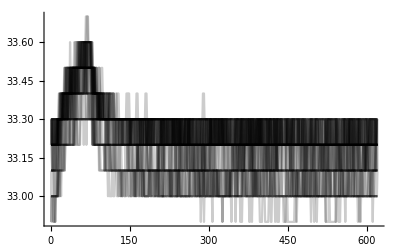
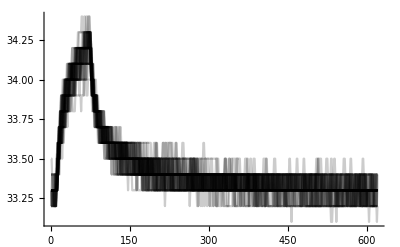
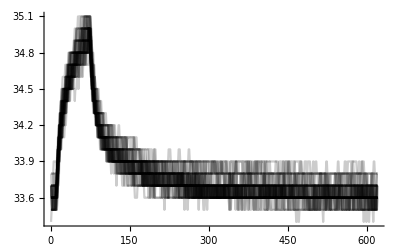
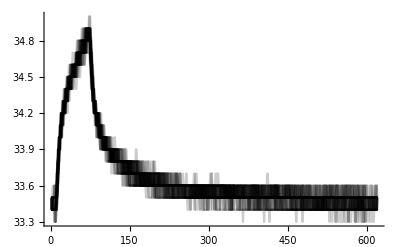

```mathematica
ListLinePlot[#,PlotStyle->Opacity[0.2,Black],PlotRange->All]&/@gagFitDataWaveLen
```

```mathematica
gagTemp=ListLinePlot[gagFitDataWaveLen[[3]],PlotStyle->Opacity[0.2,Black],PlotRange->All]
```

-Graphics-

```mathematica
Ordering[gagFitDataWaveLen[[3]][[;;, 1]],1]
```

{1}

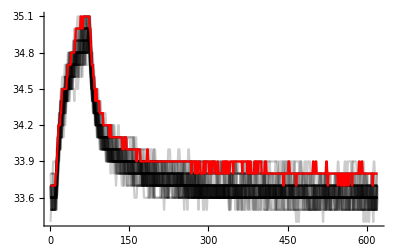

```mathematica
Show[gagTemp, ListLinePlot[gagFitDataWaveLen[[3]][[11]],PlotStyle->Red,PlotRange->All],PlotRange->All]
```

```mathematica
Dimensions/@gagFitDataWaveLen
```

{{40,620},{40,620},{40,620},{40,620}}

## Normalize Data so Baseline is at 0, Set Range Variables

```mathematica
Dimensions/@gagFitDataWaveLen
```

{{40,620},{40,620},{40,620},{40,620}}

```mathematica
gagFitDataWaveLen=baselineNormalize/@ gagFitDataWaveLen;
```

```mathematica
Dimensions/@gagFitDataWaveLen
```

{{40,620},{40,620},{40,620},{40,620}}

```mathematica
501/(1000/128.) (*figuring out stim duration*)
```

64.128

```mathematica
stimDuration=64;
stimStart=11;
stimEnd=stimStart+stimDuration;
fallStart=stimStart+stimDuration-1;
fallEnd=fallStart+200;
trialLength=Length[gagFitDataWaveLen[[1, 1]]]
```

620

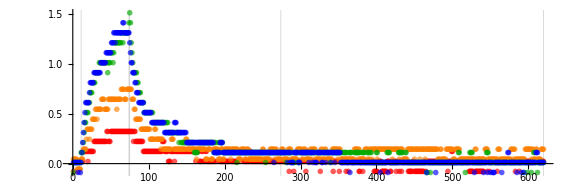

```mathematica
gagTempFitDataWaveLen=ListPlot[gagFitDataWaveLen[[All,1]],
GridLines->{{stimStart,stimEnd,fallStart,fallEnd,trialLength},None}, PlotRange->All,
AspectRatio->1/3, ImageSize->72*8,PlotStyle->gagColors]
```

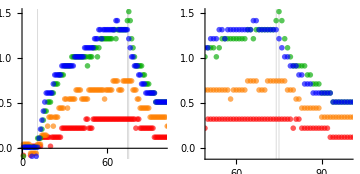

```mathematica
GraphicsRow[
{Show[gagTempFitDataWaveLen,PlotRange->{{0,100},All},AspectRatio->1],
Show[gagTempFitDataWaveLen,PlotRange->{stimStart+stimDuration+{-25,+25},All},AspectRatio->1]}, ImageSize->Medium]
```

## Cleaner Plots

```mathematica
Dimensions[Transpose[{gagFitDataWaveLen,gagColors}]]
```

{4,2}

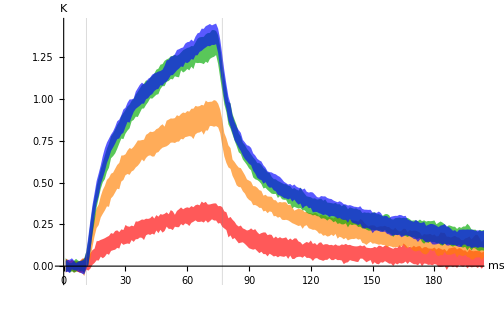

```mathematica
grSDWaveLen=Show[meanBandPlot[#[[1]],#[[2]]]& /@ Transpose[{gagFitDataWaveLen,gagColors}],
GridLines->{{stimStart,stimEnd+2},None}, PlotRange->{{0,200},All},AspectRatio->1/GoldenRatio,ImageSize->72*7, AxesLabel->{"ms", "K"},Ticks->{Automatic,Automatic}, 
AxesStyle->Thickness[0.0025], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0,0}]
```

```mathematica
legend={"473","532","589","633"};
```

```mathematica
gagLegend=Graphics[
Table[
{Reverse[gagColors][[n+1]],EdgeForm[Directive[Thin,Black]],Rectangle[{-10+n*20, 0},{10+n*20, 5}], Black, Text[legend[[n+1]],{n*20, 0},{0,1.5},BaseStyle->{FontSize->9,Bold}]}, 
{n,0,3}], PlotLabel->Style["Wavelength [nm]",FontWeight->Bold,FontColor->Black,FontSize->9], AspectRatio->1/10,ImageSize->72*1.5
]
```

-Graphics-

```mathematica
(*gagLegend=LineLegend[Reverse[gagColors],legend,LegendLayout->"Column",LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->5,LegendLayout->"Row",LegendLabel->"Wavelength [nm]"]
```

```mathematica
(*gagLegend=BarLegend[{gagColors,{0,200}},LegendMarkers-> {{20,40}},LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->5,LegendLayout->"Row",LegendLabel->"Lapsed Time [mins]"]*)
```

```mathematica
(*gagLegend=Graphics[
Table[
{gagColors[[n+1]],EdgeForm[Directive[Thin,Black]],Rectangle[{-10+n*20, 0},{10+n*20, 5}], Black, Text[legend[[n+1]],{n*20, 0},{0,1.5},BaseStyle->{FontSize->9,Bold}]}, 
{n,0,3}], PlotLabel->Style["Wavelength [nm]",FontWeight->Bold], AspectRatio->0.9/10,ImageSize->72*3
]
```

```mathematica
(*gagLegend=BarLegend[{gagColors,{-10,210}},10,LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->5,LegendLayout->"Row",LegendLabel->"Lapsed Time [mins]"]*)
```

```mathematica
(*gagLegend2= SwatchLegend[{Opacity[0.15,Blue]}, {"Laser Stimulation"},LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->{{53,54},{5,5}},LegendLayout->"Row",LegendFunction->(Framed[#]&)]*)
```

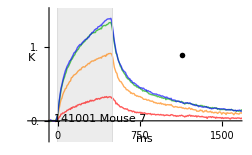

```mathematica
grSDWaveLen=Show[
Show[meanPlot[#[[1]],#[[2]],{-11,620-11}*samplingRate]& /@ Transpose[{gagFitDataWaveLen,gagColors}],ImageSize->72*3.5,
GridLines->{{stimStart-11,stimEnd-11}*samplingRate,None},GridLinesStyle->Thickness[0.0025],PlotRange->{{-30,210}*samplingRate,{-0.25,1.5}},AspectRatio->1/GoldenRatio, AxesLabel->{None, None},Ticks->{Table[n,{n,0,1500,250}],Table[n,{n,0,1.5,0.5}]},TicksStyle->Directive[Black,9],
AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{-10*samplingRate,0},LabelStyle->{FontSize->9,FontWeight->"Bold"},
Prolog->{Opacity[0.15,Gray], Rectangle[{(stimStart-11)*samplingRate,-1},{(stimEnd-11)*samplingRate,7}]},
Epilog->{Text["ms",{101*samplingRate,-0.25},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Text["K",{-30*samplingRate,0.85},BaseStyle->{FontSize->9,FontWeight->"Bold"}],
Inset[gagLegend,{145*samplingRate,0.9}],Text["141001 Mouse 7",{50*samplingRate,0.03},BaseStyle->{FontSize->2}]}]
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141001 Mouse 7(Wavelength comparison 2)

```mathematica
Export["141001.AverageWaveLen(10mW).png",grSDWaveLen,ImageResolution->600]
```

141001.AverageWaveLen(10mW).png

```mathematica
Export["141001.AverageWaveLen(10mW).pdf",grSDWaveLen,ImageResolution->600]
```

141001.AverageWaveLen(10mW).pdf

```mathematica
gagMeanDataWaveLen= Mean/@gagFitDataWaveLen;
```

```mathematica
Dimensions[gagMeanDataWaveLen]
```

{4,620}

```mathematica
gagMaxDataWaveLen=Max/@gagMeanDataWaveLen
```

{0.329444,0.914722,1.33667,1.39139}

```mathematica
gagMaxDataWaveLen=Map[ToString[NumberForm[#,{3,2}],OutputForm]&,gagMaxDataWaveLen,{1}]
```

{0.33,0.91,1.34,1.39}

```mathematica
gagMaxDataWaveLen=ToExpression[gagMaxDataWaveLen]
```

{0.33,0.91,1.34,1.39}

```mathematica
Options[BarChart]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BarOrigin→Bottom,BarSpacing→Automatic,BaselinePosition→Automatic,BaseStyle→{},ChartBaseStyle→Automatic,ChartElementFunction→Automatic,ChartElements→Automatic,ChartLabels→None,ChartLayout→Automatic,ChartLegends→None,ChartStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,Joined→False,LabelingFunction→Automatic,LabelStyle→{},LegendAppearance→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

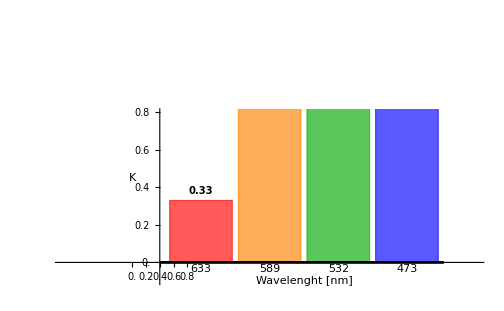

```mathematica
gagMaxTempGraph=BarChart[gagMaxDataWaveLen,
PlotRange->{{-1,5},{-0.1,0.8}},
ChartLabels->{{"633","589","532","473"}},
AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->12],Directive[Black,Thickness[0.004],FontSize->12]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->12,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,0.8,0.2}]},ChartStyle->gagColors,TicksStyle->Bold,
LabelingFunction->Above,LabelStyle->{FontWeight->Bold,FontSize->10},
Epilog->{Text["Wavelenght [nm]",{2.5,-0.1},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Text["K",{0,0.45},BaseStyle->{FontSize->12,FontWeight->"Bold"}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141001 Mouse 7(Wavelength comparison 2)

```mathematica
Export["141001.WaveLenMaxTemp(10mW).png",gagMaxTempGraph]
```

141001.WaveLenMaxTemp(10mW).png

```mathematica
Export["141001.WaveLenMaxTemp(10mW).pdf",gagMaxTempGraph]
```

141001.WaveLenMaxTemp(10mW).pdf

## Change data to {{time,value}, ....} format and Fit Functions

```mathematica
gagMakeTrialXY[data_, startPoint_Integer, endPoint_Integer]:=Module[{gagTimecourseR},
gagTimecourseR =Range[0, endPoint-startPoint ] *samplingRate;
Flatten[ 
Transpose[{gagTimecourseR,#[[startPoint;;endPoint]]}]&  /@ data,   1
]
];
```

```mathematica
gagModelModelRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc, tempShift},
Simplify[Evaluate[
NonlinearModelFit[gagMakeTrialXY[data,startPoint, endPoint],  
{0.4*a*Log[0.01*c* x+0.1*b]},
{a,b,c},x]]] 
];
```

```mathematica
gagModelShiftFactorRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc,tempShift},
tempFunc=gagModelFuncRLog[data, startPoint, endPoint];
tempShift= x /. Flatten[Solve[ Evaluate[tempFunc[x]]==0, x]];
tempShift
];
```

```mathematica
gagModelFuncRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc},
tempFunc=gagModelModelRLog[data, startPoint, endPoint]["BestFit"];
Evaluate[tempFunc /. x->#]&
];
```

```mathematica
gagModelModelFExp[data_, startPoint_Integer, endPoint_Integer]:=
Module[{},
Simplify[Evaluate[
NonlinearModelFit[gagMakeTrialXY[data,startPoint, endPoint],  
{a*ⅇ^(b*(x+7)) +aa*ⅇ^(b*bb*(x+90)),{0 < a<1,-0.3<b<-0.0001 ,0<aa<5,0<bb<1}},
{a,c,b,aa,bb,cc},x]]]
];
```

```mathematica
gagModelFuncFExp[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc},
tempFunc=gagModelModelFExp[data, startPoint, endPoint]["BestFit"] ;
Evaluate[tempFunc /. x->#]&
];
```

```mathematica
Manipulate[
Show[grSDWaveLen,Plot[a*ⅇ^(b*(x)) +aa*ⅇ^(bb*(x)),{x,fallStart,trialLength},PlotRange->All],
PlotRange->All],
{{a,230.},0,1500},{{b,-0.0612},-0.2,0.2},{{aa,0.31},0,5},{{bb,0.0075},-1,0.3}
];
```

## Fit Function BootStrap

```mathematica
gagBootStrapData=Table[RandomSample[#,10],{500}]& /@gagFitDataWaveLen;
Dimensions[gagBootStrapData]
```

{4,500,10,620}

```mathematica
gagBootStrapModel= ParallelMap[gagModelModelRLog[#,stimStart, stimEnd]&, gagBootStrapData[[#]]]& /@Range[4];
Dimensions[gagBootStrapModel]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{4,500}

```mathematica
gagBootStrapModelParams=#["BestFitParameters"]&/@gagBootStrapModel[[#]]&/@Table[x,{x,1,4,1}];
Dimensions[gagBootStrapModelParams]
```

{4,500,3}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{1,3,2}];
Dimensions[gagBootStrapModelParams]
```

{4,3,500}

```mathematica
gagBootStrapModelParams={a/.#& /@gagBootStrapModelParams[[;;,1,#]]*0.4&/@Table[x,{x,1,500,1}],b/.#& /@gagBootStrapModelParams[[;;,2,#]]*0.1&/@Table[x,{x,1,500,1}],c/.#& /@gagBootStrapModelParams[[;;,3,#]]*0.01&/@Table[x,{x,1,500,1}]};
Dimensions[gagBootStrapModelParams]
```

{3,500,4}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{1,3,2}];
Dimensions[gagBootStrapModelParams]
```

{3,4,500}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{2,1,3}];
Dimensions[gagBootStrapModelParams]
```

{4,3,500}

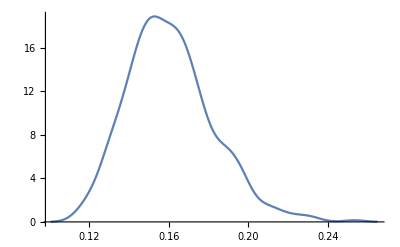
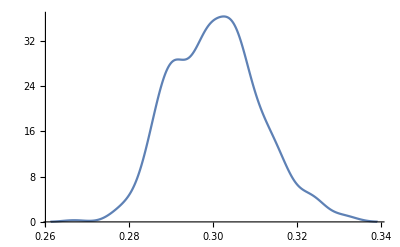
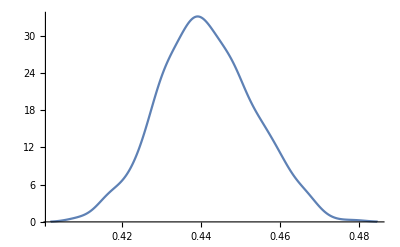
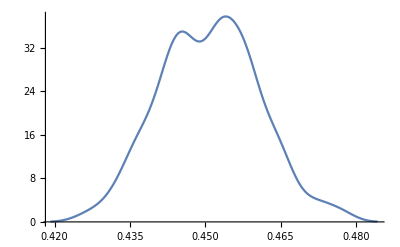
5
6[{{-Graphics-,0.0000684995},{-Graphics-,0.0996643},{-Graphics-,0.295661},{-Graphics-,0.167317}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,1]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,4,1}]//TableForm[{5,6}]
```

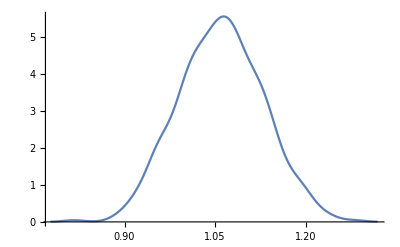
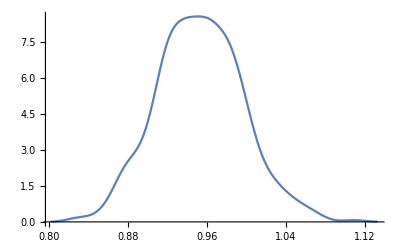
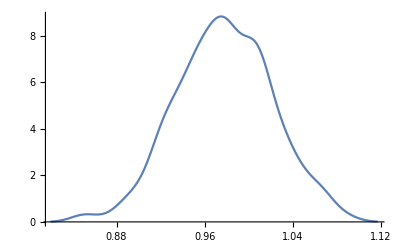
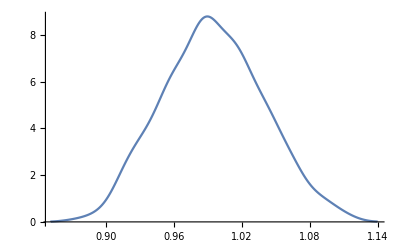
5
6[{{-Graphics-,0.0000684995},{-Graphics-,0.0996643},{-Graphics-,0.295661},{-Graphics-,0.167317}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,2]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,4,1}]//TableForm[{5,6}]
```

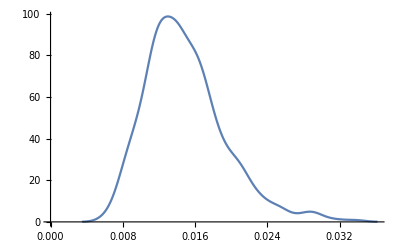
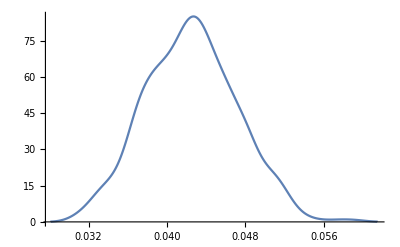
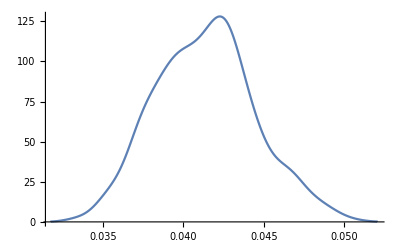
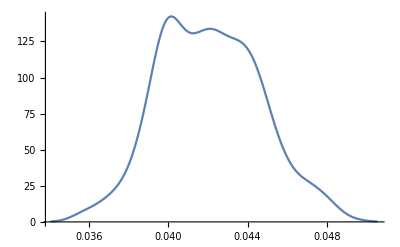
5
6[{{-Graphics-,0.0000684995},{-Graphics-,0.0996643},{-Graphics-,0.295661},{-Graphics-,0.167317}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,3]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,4,1}]//TableForm[{5,6}]
```

```mathematica
gagBootStrapModelParamsMedian=Transpose[Median[#]&/@gagBootStrapModelParams[[#]]&/@Range[4]];
Dimensions[gagBootStrapModelParamsMedian]
```

{3,4}

```mathematica
gagBootStrapModelParams99= Transpose[Quantile[#,{0.01,0.99},{{1/2,0},{0,1}}]&/@gagBootStrapModelParams[[#]]&/@Range[4],{2,1,3}];
Dimensions[gagBootStrapModelParams99]
```

{3,4,2}

```mathematica
gagBootStrapModelParamsMedian0=gagBootStrapModelParamsMedian;
```

```mathematica
gagBootStrapModelParamsMedian0={Range[4],#}&/@gagBootStrapModelParamsMedian0;
Dimensions[gagBootStrapModelParamsMedian0]
```

{3,2,4}

```mathematica
gagBootStrapModelParamsMedian0=Transpose[gagBootStrapModelParamsMedian0,{1,3,2}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

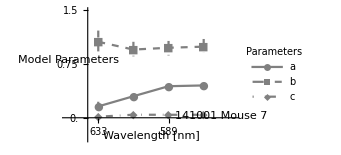

```mathematica
gagAvalueBootStrapGraph=ErrorListPlot[
Transpose[{gagBootStrapModelParamsMedian0,
Map[ErrorBar,
(gagBootStrapModelParams99-gagBootStrapModelParamsMedian0[[;;,;;,2]]),
{2}
]
},{3,1,2}],

Joined->True,ImageSize->72*3.5,
PlotRange->{{0.08,4.9},{-0.3,1.5}},AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0.7,0},LabelStyle->{FontSize->9,FontWeight->"Bold"},
PlotMarkers->{Automatic,Medium},
PlotLegends-> Placed[LineLegend[{"a","b","c"},LegendMarkers->{Automatic},LabelStyle->9,LegendMarkerSize->{20,10},LegendLabel->Style["Parameters",FontWeight->Bold,FontSize->9]],{{0.95,0.42},{0.7,0.5}}],
PlotStyle->{Gray,Directive[Gray,Dashed],Directive[Gray,DotDashed]},Ticks->{{{1,"633"},{2,"589"},{3,"589"},{4,"473"}},Table[n,{n,0,1.5,0.25}]},TicksStyle->Directive[Black,9],Epilog->{Text["Wavelength [nm]",{2.5,-0.25},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Rotate[Text["Model Parameters",{0.15,0.8},BaseStyle->{FontSize->9,FontWeight->"Bold"}],90 Degree],Text["141001 Mouse 7",{4.5,0.03},BaseStyle->{FontSize->2}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141001 Mouse 7(Wavelength comparison 2)

```mathematica
Export["141001.A-valueWaveLenBootStrap(10mW).png",gagAvalueBootStrapGraph,ImageResolution->600]
```

141001.A-valueWaveLenBootStrap(10mW).png

```mathematica
Export["141001.A-valueWaveLenBootStrap(10mW).pdf",gagAvalueBootStrapGraph,ImageResolution->600]
```

141001.A-valueWaveLenBootStrap(10mW).pdf

```mathematica
gagBootStrapModelParamsMedian0
```

{{{1,0.158572},{2,0.300502},{3,0.440493},{4,0.451299}},{{1,1.06048},{2,0.952178},{3,0.977382},{4,0.992751}},{{1,0.014242},{2,0.0424322},{3,0.0413628},{4,0.0419445}}}

```mathematica
gagBootStrapModelParamsMedian1=Transpose[Median[#]&/@gagBootStrapModelParams[[#]]&/@Range[4]]
```

{{0.158572,0.300502,0.440493,0.451299},{1.06048,0.952178,0.977382,0.992751},{0.014242,0.0424322,0.0413628,0.0419445}}

```mathematica
gagBootStrapModelParamsMedian1=ToString[NumberForm[#,{3,2}]]&/@gagBootStrapModelParamsMedian1
```

{{0.16, 0.30, 0.44, 0.45},{1.06, 0.95, 0.98, 0.99},{0.01, 0.04, 0.04, 0.04}}

```mathematica
gagBootStrapModelParamsMedian1=ToExpression[gagBootStrapModelParamsMedian1]
```

{{0.16,0.3,0.44,0.45},{1.06,0.95,0.98,0.99},{0.01,0.04,0.04,0.04}}

```mathematica
gagBootStrapModelParams991=ToString[NumberForm[#,{3,2}]]&/@gagBootStrapModelParams99
```

{{{0.12, 0.22}, {0.28, 0.33}, {0.42, 0.47}, {0.43, 0.48}},{{0.91, 1.22}, {0.86, 1.06}, {0.87, 1.07}, {0.90, 1.10}},{{0.01, 0.03}, {0.03, 0.05}, {0.04, 0.05}, {0.04, 0.05}}}

```mathematica
gagBootStrapModelParams991=ToExpression[gagBootStrapModelParams991]
```

{{{0.12,0.22},{0.28,0.33},{0.42,0.47},{0.43,0.48}},{{0.91,1.22},{0.86,1.06},{0.87,1.07},{0.9,1.1}},{{0.01,0.03},{0.03,0.05},{0.04,0.05},{0.04,0.05}}}

```mathematica
gagBootStrapModelParams991=gagBootStrapModelParams991-gagBootStrapModelParamsMedian1
```

{{{-0.04,0.06},{-0.02,0.03},{-0.02,0.03},{-0.02,0.03}},{{-0.15,0.16},{-0.09,0.11},{-0.11,0.09},{-0.09,0.11}},{{0.,0.02},{-0.01,0.01},{0.,0.01},{0.,0.01}}}

```mathematica
gagCValueBootStrapData=Table[gagBootStrapModelParamsMedian1[[i,j]]->gagBootStrapModelParams991[[i,j]],{i,1,Length[gagBootStrapModelParamsMedian1]},{j,1,Length[gagBootStrapModelParamsMedian1[[1]]]}]
```

{{0.16→{-0.04,0.06},0.3→{-0.02,0.03},0.44→{-0.02,0.03},0.45→{-0.02,0.03}},{1.06→{-0.15,0.16},0.95→{-0.09,0.11},0.98→{-0.11,0.09},0.99→{-0.09,0.11}},{0.01→{0.,0.02},0.04→{-0.01,0.01},0.04→{0.,0.01},0.04→{0.,0.01}}}

```mathematica
errorBar[type_:"Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{errorN,errorP},{errorN=Flatten[meta],errorP=Flatten[meta]};
{errorN,errorP}=If[{errorN,errorP}==={},0,Last[{errorN,errorP}]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Thickness[0.0035],Line[{{{(x0+x1)/2,y1+errorN},{(x0+x1)/2,y1+errorP}},{{1/4 (3 x0+x1),y1+errorP},{1/4 (x0+3 x1),y1+errorP}},{{1/4 (3 x0+x1),y1+errorN},{1/4 (x0+3 x1),y1+errorN}}}]}}]
```

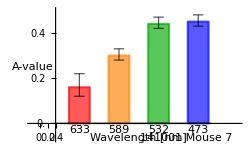

```mathematica
gagAValueBootStrapGraph=BarChart[gagCValueBootStrapData[[1]],ChartElementFunction->errorBar["Rectangle"],ImageSize->72*3.5,
PlotRange->{{-0.2,5},{-0.07,0.5}},
ChartLabels->{{"633","589","532","473"}},LabelStyle->{FontSize->9,FontWeight->"Bold"},BarSpacing->0.9,ChartBaseStyle->EdgeForm[Thickness[0.00595]],
AspectRatio->1/GoldenRatio,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->9],Directive[Black,Thickness[0.004],FontSize->9]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->9,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,0.5,0.1}]},TicksStyle->Directive[Black,9],ChartStyle->gagColors,TicksStyle->Bold,
LabelStyle->{FontWeight->Bold,FontSize->9},
Epilog->{Text["Wavelength [nm]",{2.5,-0.065},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Rotate[Text["A-value",{-0.18,0.25},BaseStyle->{FontSize->9,FontWeight->"Bold"}],90 Degree],Text["141001 Mouse 7",{3.7,-0.065},BaseStyle->{FontSize->2}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141001 Mouse 7(Wavelength comparison 2)

```mathematica
Export["141001.WaveLenA-ValueBootStrap(10mW).png",gagAValueBootStrapGraph,ImageResolution->600]
```

141001.WaveLenA-ValueBootStrap(10mW).png

```mathematica
Export["141001.WaveLenA-ValueBootStrap(10mW).pdf",gagAValueBootStrapGraph,ImageResolution->600]
```

141001.WaveLenA-ValueBootStrap(10mW).pdf

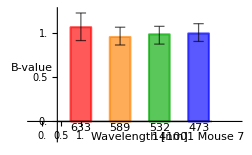

```mathematica
gagBValueBootStrapGraph=BarChart[gagCValueBootStrapData[[2]],ChartElementFunction->errorBar["Rectangle"],ImageSize->72*3.5,
PlotRange->{{-0.25,5},{-0.2,1.25}},
ChartLabels->{{"633","589","532","473"}},LabelStyle->{FontSize->9,FontWeight->"Bold"},BarSpacing->0.9,ChartBaseStyle->EdgeForm[Thickness[0.00595]],
AspectRatio->1/GoldenRatio,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->9],Directive[Black,Thickness[0.004],FontSize->9]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->9,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,1.25,0.25}]},TicksStyle->Directive[Black,9],ChartStyle->gagColors,TicksStyle->Bold,
LabelStyle->{FontWeight->Bold,FontSize->9},
Epilog->{Text["Wavelength [nm]",{2.5,-0.17},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Rotate[Text["B-value",{-0.25,0.6},BaseStyle->{FontSize->9,FontWeight->"Bold"}],90 Degree],Text["141001 Mouse 7",{4,-0.17},BaseStyle->{FontSize->2}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141001 Mouse 7(Wavelength comparison 2)

```mathematica
Export["141001.WaveLenB-ValueBootStrap(10mW).png",gagBValueBootStrapGraph,ImageResolution->600]
```

141001.WaveLenB-ValueBootStrap(10mW).png

```mathematica
Export["141001.WaveLenB-ValueBootStrap(10mW).pdf",gagBValueBootStrapGraph,ImageResolution->600]
```

141001.WaveLenB-ValueBootStrap(10mW).pdf

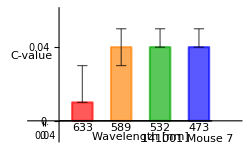

```mathematica
gagCValueBootStrapGraph=BarChart[gagCValueBootStrapData[[3]],ChartElementFunction->errorBar["Rectangle"],ImageSize->72*3.5,
PlotRange->{{-0.3,5},{-0.01,0.06}},
ChartLabels->{{"633","589","532","473"}},LabelStyle->{FontSize->9,FontWeight->"Bold"},BarSpacing->0.9,ChartBaseStyle->EdgeForm[Thickness[0.00595]],
AspectRatio->1/GoldenRatio,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->9],Directive[Black,Thickness[0.004],FontSize->9]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->9,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,0.06,0.02}]},TicksStyle->Directive[Black,9],ChartStyle->gagColors,TicksStyle->Bold,
LabelStyle->{FontWeight->Bold,FontSize->9},
Epilog->{Text["Wavelength [nm]",{2.5,-0.009},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Rotate[Text["C-value",{-0.3,0.035},BaseStyle->{FontSize->9,FontWeight->"Bold"}],90 Degree],Text["141001 Mouse 7",{3.7,-0.01},BaseStyle->{FontSize->2}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141001 Mouse 7(Wavelength comparison 2)

```mathematica
Export["141001.WaveLenC-ValueBootStrap(10mW).png",gagCValueBootStrapGraph,ImageResolution->600]
```

141001.WaveLenC-ValueBootStrap(10mW).png

```mathematica
Export["141001.WaveLenC-ValueBootStrap(10mW).pdf",gagCValueBootStrapGraph,ImageResolution->600]
```

141001.WaveLenC-ValueBootStrap(10mW).pdf

```mathematica
gagBootStrapModelParamsMedian={gagBootStrapModelParamsMedian,gagBootStrapModelParams99};
```

```mathematica
Dimensions[gagBootStrapModelParamsMedian]
```

{2,3,4}

```mathematica
gagBootStrapModelParamsMedian=Transpose[gagBootStrapModelParamsMedian,{3,1,2}]
Dimensions[gagBootStrapModelParamsMedian]
```

{{{0.158572,{0.119245,0.223605}},{0.300502,{0.278923,0.326193}},{0.440493,{0.415838,0.467638}},{0.451299,{0.428626,0.475745}}},{{1.06048,{0.909119,1.21727}},{0.952178,{0.857065,1.06057}},{0.977382,{0.869887,1.07261}},{0.992751,{0.90467,1.09993}}},{{0.014242,{0.00746572,0.0291631}},{0.0424322,{0.0324897,0.0530566}},{0.0413628,{0.0350459,0.04892}},{0.0419445,{0.0363911,0.0481375}}}}

{3,4,2}

```mathematica
gagBootStrapModelParamsMedian=Map[(ToString[NumberForm[#[[1]],{3,2}]] <> " ("<>ToString[NumberForm[#[[2,1]],{3,2}]]<>"-"<>ToString[NumberForm[#[[2,2]],{3,2}]]<>")" )&, gagBootStrapModelParamsMedian,{2}]
```

{{0.16 (0.12-0.22),0.30 (0.28-0.33),0.44 (0.42-0.47),0.45 (0.43-0.48)},{1.06 (0.91-1.22),0.95 (0.86-1.06),0.98 (0.87-1.07),0.99 (0.90-1.10)},{0.01 (0.01-0.03),0.04 (0.03-0.05),0.04 (0.04-0.05),0.04 (0.04-0.05)}}

```mathematica
gagBootStrapModelParamsMedian=Prepend[gagBootStrapModelParamsMedian,{"Wavelength [nm]",633,589,532,473}];
Dimensions[gagBootStrapModelParamsMedian]
```

{4}

```mathematica
gagBootStrapModelParamsMedian[[2]]
```

{0.16 (0.12-0.22),0.30 (0.28-0.33),0.44 (0.42-0.47),0.45 (0.43-0.48)}

```mathematica
gagBootStrapModelParamsMedian[[2]]= Prepend[gagBootStrapModelParamsMedian[[2]],"a (1%CI-99%CI)"];
```

```mathematica
gagBootStrapModelParamsMedian[[3]]= Prepend[gagBootStrapModelParamsMedian[[3]],"b (1%CI-99%CI)"];
```

```mathematica
gagBootStrapModelParamsMedian[[4]]= Prepend[gagBootStrapModelParamsMedian[[4]],"c (1%CI-99%CI)"];
```

```mathematica
Options[Grid]
```

{Alignment→{Center,Baseline},AllowedDimensions→Automatic,AllowScriptLevelChange→True,AutoDelete→False,Background→None,BaselinePosition→Automatic,BaseStyle→{},DefaultBaseStyle→Grid,DefaultElement→□,DeleteWithContents→True,Dividers→{},Editable→Automatic,Frame→None,FrameStyle→Automatic,ItemSize→Automatic,ItemStyle→None,Selectable→Automatic,Spacings→Automatic}

```mathematica
gagBootStrapModelParamsMedian//InputForm
```

{{"Wavelength [nm]", 633, 589, 532, 473}, {"a (1%CI-99%CI)", "0.16 (0.12-0.22)", "0.30 (0.28-0.33)", "0.44 (0.42-0.47)", "0.45 (0.43-0.48)"}, 
 {"b (1%CI-99%CI)", "1.06 (0.91-1.22)", "0.95 (0.86-1.06)", "0.98 (0.87-1.07)", "0.99 (0.90-1.10)"}, {"c (1%CI-99%CI)", "0.01 (0.01-0.03)", "0.04 (0.03-0.05)", "0.04 (0.04-0.05)", "0.04 (0.04-0.05)"}}

```mathematica
gagParamsTableBootStrap=Grid[gagBootStrapModelParamsMedian,Frame->All,ItemSize->{{1->9,2;;12->8},1.5},BaseStyle->{FontSize->9,FontFamily->"Helvetica"},ItemStyle->{{Bold},{Directive[Bold,FontFamily->"Helvetica"],FontFamily->"Helvetica",FontFamily->"Helvetica",FontFamily->"Helvetica"}},Dividers->{{2->Thick},{2->Thick}},Background->{None,{2->Opacity[0.35,Gray],4->Opacity[0.35,Gray]}}(*,BaseStyle{FontFamily->"Helvetica"}*)]
```

Wavelength [nm] | 633 | 589 | 532 | 473
a (1%CI-99%CI) | 0.16 (0.12-0.22) | 0.30 (0.28-0.33) | 0.44 (0.42-0.47) | 0.45 (0.43-0.48)
b (1%CI-99%CI) | 1.06 (0.91-1.22) | 0.95 (0.86-1.06) | 0.98 (0.87-1.07) | 0.99 (0.90-1.10)
c (1%CI-99%CI) | 0.01 (0.01-0.03) | 0.04 (0.03-0.05) | 0.04 (0.04-0.05) | 0.04 (0.04-0.05)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141001 Mouse 7(Wavelength comparison 2)

```mathematica
Export["141001.ParamsTableBootStrap(10mW).png",gagParamsTableBootStrap,ImageResolution->600]
```

141001.ParamsTableBootStrap(10mW).png

```mathematica
Export["141001.ParamsTableBootStrap(10mW).pdf",gagParamsTableBootStrap,ImageResolution->600]
```

141001.ParamsTableBootStrap(10mW).pdf

## Fit Function

```mathematica
{funcR1,funcR2, funcR3, funcR4}=gagModelFuncRLog[#,stimStart, stimEnd]& /@gagFitDataWaveLen
```

{0.0704154 Log[1.07219+0.0164279 #1]&,0.141488 Log[1.13104+0.0326085 #1]&,0.209116 Log[0.985892+0.0442165 #1]&,0.215537 Log[1.00818+0.051457 #1]&}

```mathematica
{modelR1,modelR2, modelR3, modelR4}=gagModelModelRLog[#,stimStart, stimEnd]& /@gagFitDataWaveLen;
```

```mathematica
gagModelParams={modelR1["BestFitParameters"],modelR2["BestFitParameters"],modelR3["BestFitParameters"],modelR4["BestFitParameters"]};
```

```mathematica
gagModelParams=Transpose[gagModelParams]
```

{{a→0.176038,a→0.35372,a→0.52279,a→0.538843},{b→10.7219,b→11.3104,b→9.85892,b→10.0818},{c→1.64279,c→3.26085,c→4.42165,c→5.1457}}

```mathematica
gagModelParams={a/.#& /@gagModelParams[[1]]*0.4,b/.#& /@gagModelParams[[2]]*0.1,c/.#& /@gagModelParams[[3]]*0.01}
```

{{0.0704154,0.141488,0.209116,0.215537},{1.07219,1.13104,0.985892,1.00818},{0.0164279,0.0326085,0.0442165,0.051457}}

```mathematica
gagModelParams0=gagModelParams
```

{{0.0704154,0.141488,0.209116,0.215537},{1.07219,1.13104,0.985892,1.00818},{0.0164279,0.0326085,0.0442165,0.051457}}

```mathematica
gagModelParams=Map[ToString[NumberForm[#,{4,3}]]&,gagModelParams,{2}]
```

{{0.070,0.141,0.209,0.216},{1.072,1.131,0.986,1.008},{0.016,0.033,0.044,0.051}}

```mathematica
gagModelParams1=ToExpression[gagModelParams]
```

{{0.07,0.141,0.209,0.216},{1.072,1.131,0.986,1.008},{0.016,0.033,0.044,0.051}}

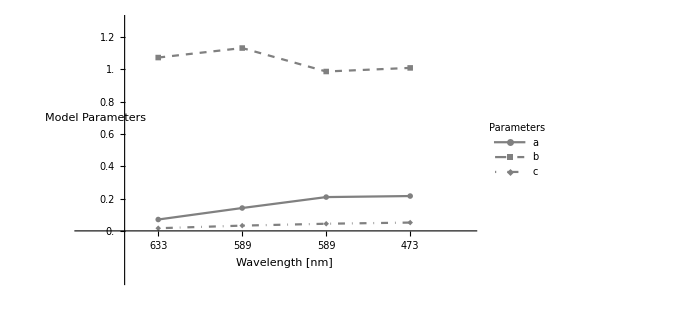

```mathematica
gagAvalueGraph=ListLinePlot[
gagModelParams0, 
PlotRange->{{0.1,4.7},{-0.3,1.3}},AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0.6,0},LabelStyle->{FontSize->12,FontWeight->"Bold"},
PlotMarkers->{Automatic,Medium},
PlotLegends-> Placed[LineLegend[{"a","b","c"},LegendMarkers->{Automatic},LegendLabel->Style["Parameters",FontWeight->Bold]],{{0.95,0.57},{0.7,0.5}}],
PlotStyle->{Gray,Directive[Gray,Dashed],Directive[Gray,DotDashed]},Ticks->{{{1,"633"},{2,"589"},{3,"589"},{4,"473"}},Table[n,{n,0,1.2,0.2}]},Epilog->{Text["Wavelength [nm]",{2.5,-0.2},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Rotate[Text["Model Parameters",{0.25,0.7},BaseStyle->{FontSize->12,FontWeight->"Bold"}],90 Degree]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141001 Mouse 7(Wavelength comparison 2)

```mathematica
Export["141001.A-valueWaveLen.png",gagAvalueGraph]
```

141001.A-valueWaveLen.png

```mathematica
Export["141001.A-valueWaveLen.pdf",gagAvalueGraph]
```

141001.A-valueWaveLen.pdf

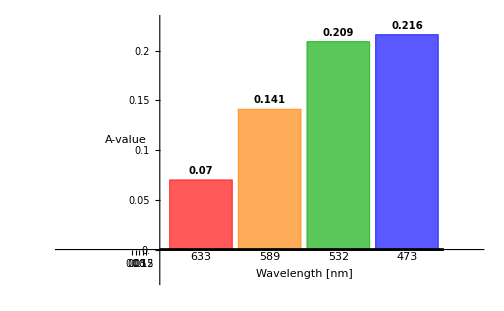

```mathematica
gagAValueGraph=BarChart[gagModelParams1[[1]],
PlotRange->{{-1,5},{-0.03,0.23}},
ChartLabels->{{"633","589","532","473"}},
AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->12],Directive[Black,Thickness[0.004],FontSize->12]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->12,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,0.2,0.05}]},ChartStyle->gagColors,TicksStyle->Bold,
LabelingFunction->Above,LabelStyle->{FontWeight->Bold,FontSize->10},
Epilog->{Text["Wavelength [nm]",{2.5,-0.025},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Rotate[Text["A-value",{-0.1,0.11},BaseStyle->{FontSize->12,FontWeight->"Bold"}],90 Degree]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141001 Mouse 7(Wavelength comparison 2)

```mathematica
Export["141001.WaveLenA-Value.png",gagAValueGraph]
```

141001.WaveLenA-Value.png

```mathematica
Export["141001.WaveLenA-Value.pdf",gagAValueGraph]
```

141001.WaveLenA-Value.pdf

```mathematica
gagModelParams=Prepend[gagModelParams,{"Wavelength [nm]",633,589,532,473}];
```

```mathematica
gagModelParams[[4]]
```

{0.016,0.033,0.044,0.051}

```mathematica
gagModelParams[[2]]= Prepend[gagModelParams[[2]],"a"];
```

```mathematica
gagModelParams[[3]]= Prepend[gagModelParams[[3]],"b"];
```

```mathematica
gagModelParams[[4]]= Prepend[gagModelParams[[4]],"c"];
```

```mathematica
gagModelParams//InputForm
```

{{"Wavelength [nm]", 633, 589, 532, 473}, {"a", "0.070", "0.141", "0.209", "0.216"}, {"b", "1.072", "1.131", "0.986", "1.008"}, {"c", "0.016", "0.033", "0.044", "0.051"}}

```mathematica
gagParamsTable=Grid[gagModelParams,Frame->All,ItemSize->{Automatic,2},ItemStyle->{{Bold},{Directive[Bold,FontFamily->"Helvetica"],FontFamily->"Helvetica",FontFamily->"Helvetica",FontFamily->"Helvetica"}},Dividers->{{2->Thick},{2->Thick}}(*,BaseStyle{FontFamily->"Helvetica"}*)]
```

Wavelength [nm] | 633 | 589 | 532 | 473
a | 0.070 | 0.141 | 0.209 | 0.216
b | 1.072 | 1.131 | 0.986 | 1.008
c | 0.016 | 0.033 | 0.044 | 0.051

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141001 Mouse 7(Wavelength comparison 2)

```mathematica
Export["141001.ParamsTable.png",gagParamsTable]
```

141001.ParamsTable.png

```mathematica
Export["141001.ParamsTable.pdf",gagParamsTable]
```

141001.ParamsTable.pdf

```mathematica
{shiftR1,shiftR2, shiftR3, shiftR4}=gagModelShiftFactorRLog[#,stimStart, stimEnd]& /@gagFitDataWaveLen
```

{-4.39417,-4.01848,0.319065,-0.159046}

```mathematica
grRPlot=Plot[{funcR1[x],funcR2[x], funcR3[x-shiftR3*samplingRate], funcR4[x-shiftR4*samplingRate]},{x,0,(stimEnd+2)*samplingRate}, PlotStyle->gagColors,PlotRange->All];
```

```mathematica
{funcF1,funcF2, funcF3, funcF4}=gagModelFuncFExp[#,fallStart, trialLength]& /@gagFitDataWaveLen
```

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {8.86389×10^-12, 0.000133779, 2.4105×10^-12}, is returned.

{0.100772 ⅇ^(-0.00906603 (7+#1))+0.0607382 ⅇ^(-0.00053615 (90+#1))&,0.247858 ⅇ^(-0.00691718 (7+#1))+0.166729 ⅇ^(-0.000869977 (90+#1))&,0.41959 ⅇ^(-0.00930312 (7+#1))+0.242396 ⅇ^(-0.00086571 (90+#1))&,0.50493 ⅇ^(-0.00835918 (7+#1))+0.217237 ⅇ^(-0.00071721 (90+#1))&}

```mathematica
grFPlot=Plot[{funcF1[x-(fallStart-stimStart)*samplingRate],funcF2[x-(fallStart-stimStart)*samplingRate], funcF3[x-(fallStart-stimStart)*samplingRate], funcF4[x-(fallStart-stimStart)*samplingRate]},{x,(fallStart-stimStart)*samplingRate,trialLength*samplingRate}, PlotStyle->gagColors,PlotRange->All];
```

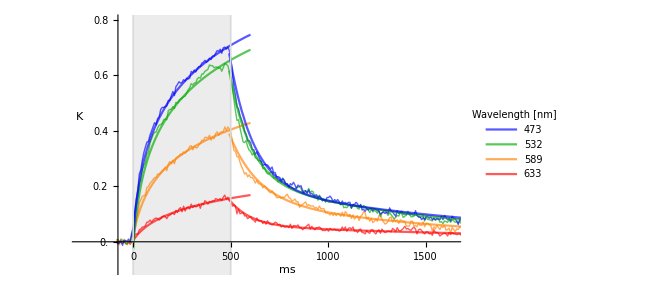

```mathematica
Show[grSDWaveLen,grRPlot,grFPlot]
```

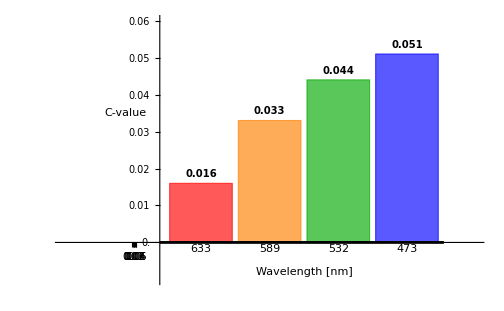

```mathematica
gagCValueGraph=BarChart[gagModelParams1[[3]],
PlotRange->{{-1,5},{-0.01,0.06}},
ChartLabels->{{"633","589","532","473"}},
AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->12],Directive[Black,Thickness[0.004],FontSize->12]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->12,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,0.06,0.01}]},ChartStyle->gagColors,TicksStyle->Bold,
LabelingFunction->Above,LabelStyle->{FontWeight->Bold,FontSize->10},
Epilog->{Text["Wavelength [nm]",{2.5,-0.008},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Rotate[Text["C-value",{-0.1,0.035},BaseStyle->{FontSize->12,FontWeight->"Bold"}],90 Degree]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141001 Mouse 7(Wavelength comparison 2)

```mathematica
Export["141001.WaveLenC-Value.png",gagCValueGraph]
```

141001.WaveLenC-Value.png

```mathematica
Export["141001.WaveLenC-Value.pdf",gagCValueGraph]
```

141001.WaveLenC-Value.pdf

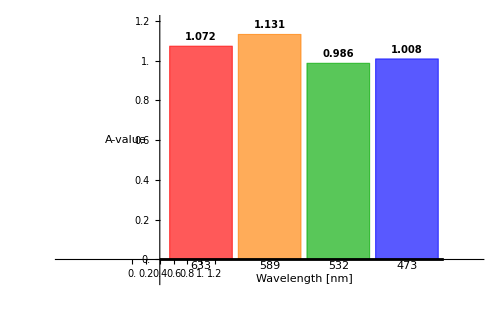

```mathematica
gagBValueGraph=BarChart[gagModelParams1[[2]],
PlotRange->{{-1,5},{-0.1,1.2}},
ChartLabels->{{"633","589","532","473"}},
AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->12],Directive[Black,Thickness[0.004],FontSize->12]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->12,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,1.2,0.2}]},ChartStyle->gagColors,TicksStyle->Bold,
LabelingFunction->Above,LabelStyle->{FontWeight->Bold,FontSize->10},
Epilog->{Text["Wavelength [nm]",{2.5,-0.1},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Rotate[Text["A-value",{-0.1,0.6},BaseStyle->{FontSize->12,FontWeight->"Bold"}],90 Degree]}
]
```